```mathematica
(*C++*)
lo[n_]:=(
in=Flatten@Import[NotebookDirectory[]<>"../out/build/x64-Debug/dgesl_in"<>ToString[n]<>".txt","Table"];
aIn=Transpose@Partition[in[[1;;8^2]],8];
ipvtIn=in[[8^2+1;;8^2+8]];
bIn=in[[8^2+8+1;;8^2+16]];
)
Manipulate[lo[n];MatrixForm@aIn,{n,1,16,1}]
```

```mathematica
(*Fortran*)
lo[n_]:=(
in=Flatten@Import[NotebookDirectory[]<>"../original/dgesl_in"<>ToString[n]<>".txt","Table"];
aIn=Transpose@Partition[in[[1;;8^2]],8];
ipvtIn=in[[8^2+1;;8^2+8]];
bIn=in[[8^2+8+1;;8^2+16]];
)
Manipulate[lo[n];MatrixForm@aIn,{n,1,55,1}]
```

```mathematica
in=Flatten@Import[NotebookDirectory[]<>"../out/build/x64-Debug/dgesl_in.txt","Table"];
aIn=Transpose@Partition[in[[1;;8^2]],8];
ipvtIn=in[[8^2+1;;8^2+8]];
bIn=in[[8^2+8+1;;8^2+16]];

out=Flatten@Import[NotebookDirectory[]<>"../out/build/x64-Debug/dgesl_out.txt","Table"];
aOut=Transpose@Partition[out[[1;;8^2]],8];
ipvtOut=out[[8^2+1;;8^2+8]];
bOut=out[[8^2+8+1;;8^2+16]];
```

```mathematica
aIn==aOut//Simplify
ipvtIn==ipvtOut//Simplify
```

True

True

```mathematica
bIn
bOut
```

{0,0.0138864,0,0.0660019,0,0.133998,0,0.186114}

{0.000096819,0.0139445,0.00046018,0.066278,0.000934266,0.134559,0.00129763,0.186892}

```mathematica
prev=Flatten@Import[NotebookDirectory[]<>"../out/build/x64-Debug/dgesl_prev.txt","Table"];
aPrev=Transpose@Partition[prev[[1;;8^2]],8];

aPrev//MatrixForm
aIn//MatrixForm
aInF//MatrixForm
```

(1 | -0.0173927 | 0 | 0.00532084 | 0 | -0.00252549 | 0 | 0.00071103
0 | 0.989564 | 0 | 0.0031925 | 0 | -0.0015153 | 0 | 0.000426618
0 | 0.0835395 | 1 | 0.0255566 | 0 | -0.0121303 | 0 | 0.00341516
0 | 0.0501237 | 0 | 1.01533 | 0 | -0.00727815 | 0 | 0.0020491
0 | 0.169603 | 0 | -0.0511019 | 1 | -0.0242551 | 0 | 0.00682881
0 | 0.101762 | 0 | -0.0306611 | 0 | 0.985447 | 0 | 0.00409728
0 | 0.235566 | 0 | -0.0709768 | 0 | 0.0341861 | 1 | 0.00962479
0 | 0.14134 | 0 | -0.0425861 | 0 | 0.0205117 | 0 | 1.00577)

(1 | -0.0173927 | 0 | 0.00532084 | 0 | -0.00252549 | 0 | 0.00071103
0 | 0.989564 | 0 | 0.0031925 | 0 | -0.0015153 | 0 | 0.000426618
0 | 0.0835395 | 1 | 0.0255566 | 0 | -0.0121303 | 0 | 0.00341516
0 | 0.0501237 | 0 | 1.01533 | 0 | -0.00727815 | 0 | 0.0020491
0 | 0.169603 | 0 | -0.0511019 | 1 | -0.0242551 | 0 | 0.00682881
0 | 0.101762 | 0 | -0.0306611 | 0 | 0.985447 | 0 | 0.00409728
0 | 0.235566 | 0 | -0.0709768 | 0 | 0.0341861 | 1 | 0.00962479
0 | 0.14134 | 0 | -0.0425861 | 0 | 0.0205117 | 0 | 1.00577)

(1. | -0.00869637 | 0. | 0.00266042 | 0. | -0.00126275 | 0. | 0.000355515
0. | 0.994813 | 0. | 0.00158686 | 0. | -0.000753192 | 0. | 0.000212055
0. | 0.0189099 | 1. | -0.0162736 | 0. | 0.0027738 | 0. | -0.00066954
0. | 0.011294 | 0. | 0.990281 | 0. | 0.00165666 | 0. | -0.000399885
0. | 0.0168064 | 0. | 0.0357158 | 1. | -0.0162571 | 0. | 0.00140835
0. | 0.0100531 | 0. | 0.0213641 | 0. | 0.990275 | 0. | 0.000842435
0. | 0.0178408 | 0. | 0.0316236 | 0. | 0.0355747 | 1. | -0.00867526
0. | 0.0106826 | 0. | 0.0189354 | 0. | 0.0213012 | 0. | 0.994805)

```mathematica
ipvtIn//MatrixForm
ipvtInF//MatrixForm
```

(1
2
3
4
5
6
7
8)

(1
2
3
4
5
6
7
8)

```mathematica
bIn//MatrixForm
bInF//MatrixForm
```

(0
0.0138864
0
0.0660019
0
0.133998
0
0.186114)

(0.
0.0138864
0.
0.0660019
0.
0.133998
0.
0.186114)

```mathematica
inF=Flatten@Import[NotebookDirectory[]<>"../original/dgesl_in.txt","Table"];
aInF=Transpose@Partition[inF[[1;;8^2]],8];
ipvtInF=inF[[8^2+1;;8^2+8]];
bInF=inF[[8^2+8+1;;8^2+16]];

outF=Flatten@Import[NotebookDirectory[]<>"../original/dgesl_out.txt","Table"];
aOutF=Transpose@Partition[outF[[1;;8^2]],8];
ipvtOutF=outF[[8^2+1;;8^2+8]];
bOutF=outF[[8^2+8+1;;8^2+16]];
```

```mathematica
aInF==aOutF//Simplify
ipvtInF==ipvtOutF//Simplify
```

True

True

```mathematica
aIn//MatrixForm
aInF//MatrixForm
```

(1 | -0.0173927 | 0 | 0.00532084 | 0 | -0.00252549 | 0 | 0.00071103
0 | 0.989564 | 0 | 0.0031925 | 0 | -0.0015153 | 0 | 0.000426618
0 | 0.0835395 | 1 | 0.0255566 | 0 | -0.0121303 | 0 | 0.00341516
0 | 0.0501237 | 0 | 1.01533 | 0 | -0.00727815 | 0 | 0.0020491
0 | 0.169603 | 0 | -0.0511019 | 1 | -0.0242551 | 0 | 0.00682881
0 | 0.101762 | 0 | -0.0306611 | 0 | 0.985447 | 0 | 0.00409728
0 | 0.235566 | 0 | -0.0709768 | 0 | 0.0341861 | 1 | 0.00962479
0 | 0.14134 | 0 | -0.0425861 | 0 | 0.0205117 | 0 | 1.00577)

(1. | -0.0173927 | 0. | 0.00532084 | 0. | -0.00252549 | 0. | 0.00071103
0. | 0.989564 | 0. | 0.0031925 | 0. | -0.0015153 | 0. | 0.000426618
0. | 0.0380204 | 1. | -0.0324859 | 0. | 0.00551847 | 0. | -0.00133088
0. | 0.0228122 | 0. | 0.980508 | 0. | 0.00331108 | 0. | -0.000798528
0. | 0.033791 | 0. | 0.0720878 | 1. | -0.0324198 | 0. | 0.00279499
0. | 0.0202746 | 0. | 0.0432527 | 0. | 0.980548 | 0. | 0.00167699
0. | 0.0358708 | 0. | 0.0638184 | 0. | 0.0717745 | 1. | -0.017308
0. | 0.0215225 | 0. | 0.0382911 | 0. | 0.0430647 | 0. | 0.989615)

```mathematica
(aIn-aInF)/(aInF+0.000000001)//MatrixForm
```

(0. | -2.42957×10^-6 | 0. | 7.48566×10^-7 | 0. | -1.00491×10^-6 | 0. | 8.83799×10^-8
0. | -3.57967×10^-7 | 0. | -5.44106×10^-7 | 0. | 2.91498×10^-6 | 0. | 4.86435×10^-8
0. | 1.19723 | 0. | -1.7867 | 0. | -3.19813 | 0. | -3.56609
0. | 1.19723 | 0. | 0.0355137 | 0. | -3.19812 | 0. | -3.5661
0. | 4.01917 | 0. | -1.70888 | 0. | -0.251842 | 0. | 1.44323
0. | 4.01918 | 0. | -1.70888 | 0. | 0.00499605 | 0. | 1.44323
0. | 5.56706 | 0. | -2.11217 | 0. | -0.523702 | 0. | -1.55609
0. | 5.56708 | 0. | -2.11217 | 0. | -0.523701 | 0. | 0.0163243)

```mathematica
bInF
bIn
bOut
bOutF
```

{0.,0.0138864,0.,0.0660019,0.,0.133998,0.,0.186114}

{0,0.0138864,0,0.0660019,0,0.133998,0,0.186114}

{0.000096819,0.0139445,0.00046018,0.066278,0.000934266,0.134559,0.00129763,0.186892}

{0.0000966826,0.0139444,0.00220717,0.0673262,0.00922326,0.139532,0.0179822,0.196903}

```mathematica
cppData=Import[NotebookDirectory[]<>"../out/build/x64-Debug/state_cpp.txt","Table"];
cppData//TableForm
f77Data=Import[NotebookDirectory[]<>"../original/state_f77.txt","Table"];
f77Data//TableForm
```

1.11022×10^-14 | 6 | -1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 0 | 0 | 0 | 0 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4 | 2 | 0 | 2 | 2 | 8 | 8 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
5 | -858993460 | 59 | -858993460 | -858993460 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 1 | 3 | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 |  |  |  |  |  |  |  |  | 
0 | 1 | -858993460 | -858993460 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
1 | -858993460 | 40 | 0 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0.0001 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 |  |  |  |  |  |  |  |  | 
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 |  |  |  |  |  |  |  |  | 
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 |  |  |  |  |  |  |  |  | 
0.0001 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 |  |  |  |  |  |  |  |  | 
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 |  |  |  |  |  |  |  |  | 
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 |  |  |  |  |  |  |  |  | 
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 |  |  |  |  |  |  |  |  |

5.42101×10^-18 | 6 | -1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0. | 0. | 0. | 0. | 0. | 0. | 0. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
4 | 1 | 0 | 1 | 1 | 4 | 4 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
5 | 0 | 158 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 1 | 3 | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. |  |  |  |  |  |  |  |  | 
0. | 1. | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 0 | 40 | 0 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. |  |  |  |  |  |  |  |  | 
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. |  |  |  |  |  |  |  |  | 
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. |  |  |  |  |  |  |  |  | 
0.1 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. |  |  |  |  |  |  |  |  | 
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. |  |  |  |  |  |  |  |  | 
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 |  |  |  |  |  |  |  |  | 
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 |  |  |  |  |  |  |  |  |

```mathematica
N@((cppData-f77Data)/(f77Data+10^-20))//TableForm
```

2043.23 | 0. | 0. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0. | 0. | 0. | 0. | 0. | 0. | 0. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1. | 0. | 1. | 1. | 1. | 1. | 0. | 0. | 1.×10^20 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0. | -8.58993×10^28 | -0.626582 | -8.58993×10^28 | -8.58993×10^28 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0. | 0. | 0. | 0. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0. | 1.×10^20 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. |  |  |  |  |  |  |  |  | 
0. | 0. | -8.58993×10^28 | -8.58993×10^28 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
1.×10^20 | -8.58993×10^28 | 0. | 0. | 0. | 0. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
1.×10^16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. |  |  |  |  |  |  |  |  | 
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. |  |  |  |  |  |  |  |  | 
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. |  |  |  |  |  |  |  |  | 
-0.999 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. |  |  |  |  |  |  |  |  | 
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. |  |  |  |  |  |  |  |  | 
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. |  |  |  |  |  |  |  |  | 
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. |  |  |  |  |  |  |  |  |

```mathematica
D[Sin[0.6*f'[x]]+x,f[x]]
```

0

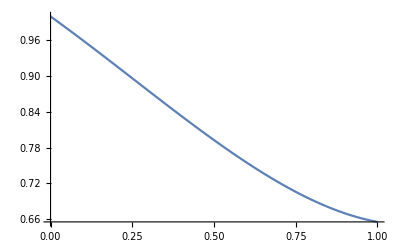

```mathematica
eq=f''[x]==Sin[0.6*f'[x]]+x;
bc={f[0]==1,f'[1]==-0.1};
sol=NDSolve[{eq,bc},f,{x,0,1}];
psol=Plot[f[x]/.sol,{x,0,1}]
```

{11,2}

{11,2}

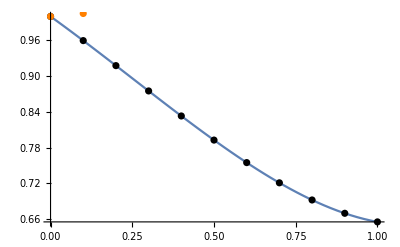

```mathematica
coldaeData=Import[NotebookDirectory[]<>"../original/result.txt","Table"];
coldaeData//Dimensions
coldaeppData=Import[NotebookDirectory[]<>"../out/build/x64-Debug/result_cpp.txt","Table"];
coldaeppData//Dimensions
Show[psol,ListPlot[coldaeData,PlotStyle->Black],ListPlot[coldaeppData,PlotStyle->Orange]]
```

```mathematica
(4.138313454292289*10^-15)^0.2
```

0.00132851

Torus Problem from https://reference.wolfram.com/language/tutorial/NDSolveDAE.html#1220709306
-Graphics-

```mathematica
(*Define parameters and functions to use for the solution:*)
Clear[x,y,z,r,ρ,c1,x1,x2,x3,u1,u2,u3,λ,eqns,vars,exactTorusSol,torusSol,ics];
r=10;
ρ=5;
c1=(1-r/Sqrt[x1[t]^2+x2[t]^2]);
```

```mathematica
(*Define the system equations and variables:*)
eqns=({{x1'[t]==u1[t]},{x2'[t]==u2[t]},{x3'[t]==u3[t]},{u1'[t]==u3[t] Cos[t]-x3[t] Sin[t]-u2[t]+2 c1 x1[t] λ[t]},{u2'[t]==u3[t] Sin[t]+x3[t] Cos[t]+u1[t]+2 c1 x2[t] λ[t]},{u3'[t]==-x3[t]+2 x3[t] λ[t]},{x1[t]^2+x2[t]^2+x3[t]^2-2 r Sqrt[x1[t]^2+x2[t]^2]+r^2-ρ^2==0}});
vars={x1,x2,x3,u1,u2,u3,λ};

(*Solve and visualize the system:*)
torusSol=NDSolve[{eqns,ics},vars,{t,0,10 Pi}]
```

NDSolve::index: The DAE solver failed at t = 0.. The solver is intended for index 1 DAE systems and structural analysis indicates that the DAE index is 3. The option Method->{"IndexReduction"->Automatic} may be used to reduce the index of the system.

{{x1→InterpolatingFunction[…],x2→InterpolatingFunction[…],x3→InterpolatingFunction[…],u1→InterpolatingFunction[…],u2→InterpolatingFunction[…],u3→InterpolatingFunction[…],λ→InterpolatingFunction[…]}}

```mathematica
(*An exact solution is known:*)
exactTorusSol={(ρ*Cos[2 Pi-t]+r)*Cos[t],(ρ Cos[2 Pi-t]+r) Sin[t],(ρ Sin[2 Pi-t])};
ics=Thread[Through[vars[[1;;-2]][0]]==Flatten[{exactTorusSol,D[exactTorusSol,t]}]/. t->0]
```

{x1[0]==15,x2[0]==0,x3[0]==0,u1[0]==0,u2[0]==15,u3[0]==-5}

```mathematica
(*Solve and visualize the system:*)
torusSol=NDSolve[{eqns,ics},vars,{t,0,10 Pi},Method->{"IndexReduction"->{Automatic,"IndexGoal"->0},"EquationSimplification"->"Residual"}]
```

{{x1→InterpolatingFunction[…],x2→InterpolatingFunction[…],x3→InterpolatingFunction[…],u1→InterpolatingFunction[…],u2→InterpolatingFunction[…],u3→InterpolatingFunction[…],λ→InterpolatingFunction[…]}}

```mathematica
ParametricPlot3D[Evaluate[{x1[t],x2[t],x3[t]}/. torusSol],{t,0,10 Pi}]
```

-Graphics3D-

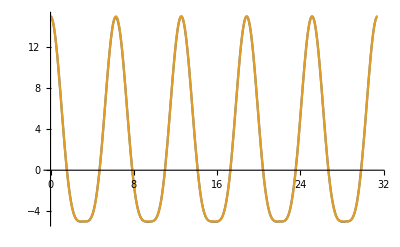
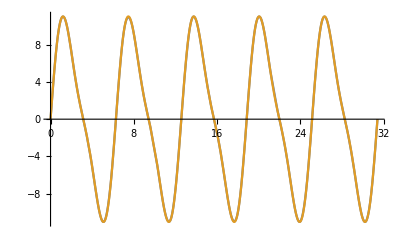
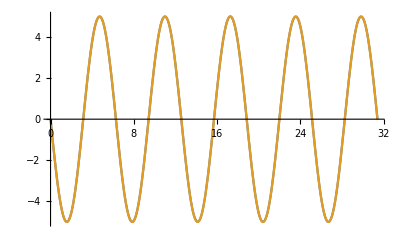

```mathematica
(*Compare the analytic and computed solutions:*)
errors=Transpose[{({x1[t],x2[t],x3[t]}/. First@torusSol),exactTorusSol}];
Plot[Evaluate[#],{t,0,10 Pi}]&/@errors
```

```mathematica
eqs={f1''[t]==f2'[t]*t,
f2''[t]==f1'[t]*t^2+f2'[t],
f1[t]+f2[t]==3
};
vars={f1,f2};
bc={f1[0]==1,f1'[0]==1,
f2'[0]==1};
sol=NDSolve[{eqs,bc},vars,{t,0,1}]
```

NDSolve::overdet: There are fewer dependent variables, {f1[t],f2[t]}, than equations, so the system is overdetermined.

NDSolve[{{f1''[t]==t f2'[t],f2''[t]==t^2 f1'[t]+f2'[t],f1[t]+f2[t]==3},{f1[0]==1,f1'[0]==1,f2'[0]==1}},{f1,f2},{t,0,1}]

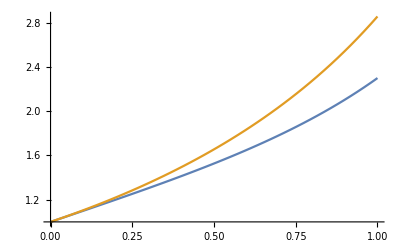

```mathematica
Plot[Evaluate[#[t]&/@vars/.sol],{t,0,1}]
```

```mathematica
DAE=({{Derivative[1][Subscript[x,1]][t]==Subscript[x,3][t]},{Subscript[x,2][t] (1-Subscript[x,2][t])==0},{Subscript[x,1][t] Subscript[x,2][t]+Subscript[x,3][t] (1-Subscript[x,2][t])==t}});
```

```mathematica
sol=NDSolve[{DAE,Subscript[x,2][0]==1},{Subscript[x,1],Subscript[x,2],Subscript[x,3]},{t,0,1}]
```

{{x_1→InterpolatingFunction[…],x_2→InterpolatingFunction[…],x_3→InterpolatingFunction[…]}}

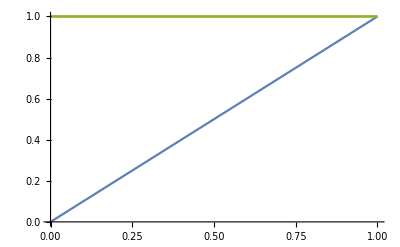

```mathematica
Plot[Evaluate[{Subscript[x,1][t],Subscript[x,2][t],Subscript[x,3][t]}/. First[sol]],{t,0,1}]
```

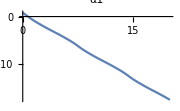
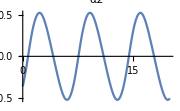
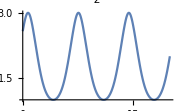
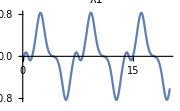
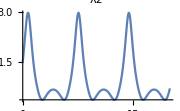

```mathematica
Clear[J1,J2,m1,m2,m3,L1,L2,LM,g,Fs,s1,LHS,RHS,eqns,contraints,vars,SliderCrankSol];
vars={α1,α2,z,λ1,λ2};
Fs[t]:=-1;
s1=Sin[α1[t]-α2[t]];
c1=Cos[α1[t]-α2[t]];
LM=(L1 L2 m2)/2;
eqns={(J1+m2 L1^2) α1''[t]+LM c1 α2''[t]==-LM s1 α2'[t]^2-(L1 Cos[α1[t]] λ1[t]+L1 Sin[α1[t]] λ2[t]),LM c1 α1''[t]+J2 α2''[t]==LM s1 α1'[t]^2-(L2 Cos[α2[t]] λ1[t]+L2 Sin[α2[t]] λ2[t]),m3 z''[t]==-Fs[t]-λ2[t]};
constraints=({{L1 Sin[α1[t]]+L2 Sin[α2[t]]==0},{z[t]-L1 Cos[α1[t]]-L2 Cos[α2[t]]==0}});
paramsFSC={J1->4.5,J2->5.5,m1->1,m2->1,m3->1,L1->1,L2->2,g->9.81};
{sliderCrank}=NDSolve[{eqns,constraints,α1[0]==Pi/4,α1'[0]==-1}/. paramsFSC,vars,{t,0,20},Method->{"IndexReduction"->Automatic}];
Row[Plot[Evaluate[#[t]/. sliderCrank],{t,0,20},PlotRange->All,PlotLabel->#,ImageSize->Small]&/@vars]
```

```mathematica
{sliderCrank}=NDSolve[{eqns,constraints,α1[0]==Pi/4,α1'[0]==-1}/. paramsFSC,vars,{t,0,20}]
```

NDSolve::index: The DAE solver failed at t = 0.. The solver is intended for index 1 DAE systems and structural analysis indicates that the DAE index is 3. The option Method->{"IndexReduction"->Automatic} may be used to reduce the index of the system.

{{α1→InterpolatingFunction[…],α2→InterpolatingFunction[…],z→InterpolatingFunction[…],λ1→InterpolatingFunction[…],λ2→InterpolatingFunction[…]}}

```mathematica
bar[loc_:{0,0},rotate_:0,scale_:1,length_:1,width_:.1,color_:Hue[.6,.2,.9]]:=Module[{},GraphicsGroup[{Rotate[{color,EdgeForm[Directive[Black,AbsoluteThickness[.5]]],(*polygon instead of rounded rectangle in case texture is needed*)Polygon[Flatten[{Table[loc+scale {width Sin[a Pi],width Cos[a Pi]},{a,1,2,1/16}],Table[{length,0}+loc+scale {width Sin[a Pi],width Cos[a Pi]},{a,0,1,1/16}]},1]],AbsolutePointSize[5],Black,Point[loc],Point[loc+scale {length,0}]},rotate Degree,loc]}]]
barFlange[loc_:{0,0},rotate_:0,scale_:1,length_:1,width_:.1,size1_:1,size2_:1,color_:Hue[.6,.2,.9]]:=Module[{},GraphicsGroup[{Rotate[{color,EdgeForm[Directive[Black,AbsoluteThickness[.5]]],Polygon[{loc+scale {0,-width size1},loc+scale {0,width size1},loc+scale {length,width size2},loc+scale {length,-width size2}}],Lighter[color,.5],Disk[loc,scale width size1],Disk[loc+scale {length,0},scale width size2],(*pins*)Gray,Disk[loc,.4 scale width size1],Disk[loc+scale {length,0},.4 scale width size2]},rotate Degree,loc]}]]
dimensionLine[loc_:{0,0},rotate_:0,scale_:1,text_:"1",length_:1,offset_:{0,0}]:=Module[{},GraphicsGroup[{Rotate[{Black,AbsoluteThickness[.5],Line[{offset+loc+scale {0,0},offset+loc+scale {0,.1}}],Arrowheads[{-Small,Small}],Arrow[{offset+loc+scale {0,.05},offset+loc+scale {length,.05}}],Line[{offset+loc+scale {length,0},offset+loc+scale {length,.1}}],Text[text,offset+loc+scale {length/2,.05},Background->White]},rotate Degree,loc]}]]
fixedHinge[loc_:{0,0},rotate_:0,scale_:1]:=Module[{},GraphicsGroup[{Rotate[{GrayLevel[.85],EdgeForm[Directive[Black,AbsoluteThickness[.5]]],Polygon[Flatten[{{loc+scale {-.25,-.5}},Table[loc+scale {.15 Sin[a Pi],.15 Cos[a Pi]},{a,1.55,2.45,.9/16}],{loc+scale {.25,-.5}}},1]],GrayLevel[.7],EdgeForm[],Rectangle[loc+scale {-.5,-.75},loc+scale {.5,-.5}],Black,AbsoluteThickness[.5],Line[{loc+scale {-.5,-.5},loc+scale {.5,-.5}}],AbsolutePointSize[5],Black,Point[{0,0}]},rotate Degree,loc]}]]
slider[loc_:{0,0},rotate_:0,scale_:1,length_:1,width_:.1,fixedLength_:2,pos_:{0,0},color_:Hue[0,.2,.9]]:=Module[{},GraphicsGroup[{Rotate[{color,EdgeForm[{Black,AbsoluteThickness[.5]}],Rectangle[loc+pos+scale {-length,-width},loc+pos+scale {length,width}],GrayLevel[.7],EdgeForm[],Rectangle[loc+scale {-fixedLength length,-width-.25},loc+scale {fixedLength length,-width}],Black,AbsoluteThickness[.5],Line[{loc+scale {-fixedLength length,-width},loc+scale {fixedLength length,-width}}],GrayLevel[.7],EdgeForm[],Rectangle[loc+scale {-fixedLength length,width+.25},loc+scale {fixedLength length,width}],Black,AbsoluteThickness[.5],Line[{loc+scale {-fixedLength length,width},loc+scale {fixedLength length,width}}]},rotate Degree,loc]}]]
```

```mathematica
Animate[rotate=(α1[t]/. sliderCrank)*(180/Pi);
f1=Graphics[{Red,Line[Map[Function[Evaluate[{#,λ1[#]}/. sliderCrank]],Range[0,t,0.025]]]}];
f2=Graphics[{Blue,Line[Map[Function[Evaluate[{#,λ2[#]}/. sliderCrank]],Range[0,t,0.025]]]}];
{bLength,bfLength}=({L1,L2}/. paramsFSC)*0.3;
Column[{Graphics[{(*parts*)bfAngle=ArcSin[bLength Cos[(90-rotate) °]/bfLength]*180/Pi;
sliderLoc={bLength Cos[rotate Pi/180]+bfLength Cos[bfAngle °],0};
slider[{.7,0},0,.2,.7,.3,3.5,sliderLoc-{.7,0},Hue[.05,.3,.9]],bar[{0,0},rotate,1,bLength,.04,Hue[.6,.2,.7]],fixedHinge[{0,0},0,.2],bfLoc={bLength Sin[(90-rotate) °],bLength Cos[(90-rotate) °]};
barFlange[bfLoc,-bfAngle,1,bfLength,.04,2,1.2,Hue[.6,.2,.9]],(*axis*)Black,AbsoluteThickness[.5],Arrowheads[Medium],Arrow[{{-.25,0},{.5,0}}],(*x*)Arrow[{{0,-.05},{0,.5}}],(*y*)(*dimensions*)
,(*force arrow*)Opacity[1],Hue[0,1,.8],AbsoluteThickness[2],Arrowheads[Medium],Arrow[{sliderLoc+{.35,0},sliderLoc+{.15,0}}],Black,Text[Style["F(t)",12,Italic],sliderLoc+{.37,0},{-1,0}]},PlotRange->{{-.5,1.5},{-.5,.5}},ImageSize->400],Show[f1,f2,Frame->True,PlotRange->{{0,10},{-2,4}},PlotLabel->Row[{Style["Tension in slider (λ1)",14,Red],"        ",Style["Tension in rod (λ2)",14,Blue]}],ImageSize->300]},Alignment->Center],{t,0,10},SaveDefinitions->True,AnimationRunning->False]
```

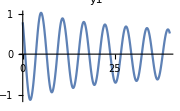
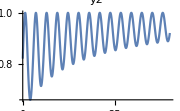
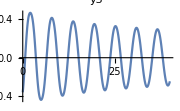
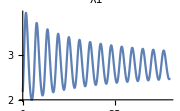
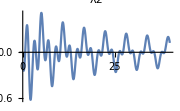

```mathematica
Clear[c,L0,Lp,a,J1,J2,m1,m2,k,L,Lp,f,F,LHS,RHS1,RHS2,y1,y2,y3,λ1,λ2,eqns,constraints,vars,SliderCrankSol2,sol];
vars={y1,y2,y3,λ1,λ2};
F[t_]:=2;
L=Sqrt[y2[t]^2-y2[t] (Cos[y3[t]]+a Cos[y1[t]])+(1+a^2)/4+a Cos[y3[t]-y1[t]]/2];
Lp=1/(2 L) (2 y2[t] y2'[t]-y2'[t] (Cos[y3[t]]+a Cos[y1[t]])+y2[t] (Sin[y3[t]] y3'[t]+a Sin[y1[t]] y1'[t])-a Sin[y3[t]-y1[t]] (y3'[t]-y1'[t])/2);
f=k*(L-L0)+c Lp;
eqns={J1 y1''[t]==-((a f (Sin[1/2 (-y1[t]+y3[t])]+Sin[y1[t]] y2[t]))/(2 L))-1/2 Sin[y1[t]] λ1[t]-1/2 Cos[y1[t]] λ2[t],m2 y2''[t]==F[t]+(f (1/2 a Cos[y1[t]]+1/2 Cos[y3[t]]-y2[t]))/L-λ1[t],J2 y3''[t]==-F[t] Sin[y3[t]]-(f (1/2 a Sin[y1[t]-y3[t]]+Sin[y3[t]] y2[t]))/(2 L)-1/2 Sin[y3[t]] λ1[t]-Cos[y3[t]] λ2[t]};
constraints=({{y2[t]-a Cos[y1[t]]-a Cos[y3[t]]==0},{a Sin[y1[t]]+Sin[y3[t]]==0}});
paramsFlexSC={a->1/2,J1->1,J2->2,m1->1,m2->1,L0->1,k->1,c->4};
SliderCrankSol2=First@NDSolve[{eqns,constraints,y1[0]==Pi/4,y1'[0]==-1}/. paramsFlexSC,vars,{t,0,40},Method->"IndexReduction"->Automatic];
Row[Plot[Evaluate[#[t]/. SliderCrankSol2],{t,0,40},PlotRange->All,PlotLabel->#,ImageSize->Small]&/@vars]
```

```mathematica
First@NDSolve[{eqns,constraints,y1[0]==Pi/4,y1'[0]==-1}/. paramsFlexSC,vars,{t,0,40},Method->"IndexReduction"->None];
```

NDSolve::index: The DAE solver failed at t = 0.. The solver is intended for index 1 DAE systems and structural analysis indicates that the DAE index is 3. The option Method->{"IndexReduction"->Automatic} may be used to reduce the index of the system.

```mathematica
bar[loc_:{0,0},rotate_:0,scale_:1,length_:1,width_:.1,color_:Hue[.6,.2,.9]]:=Module[{},GraphicsGroup[{Rotate[{color,EdgeForm[Directive[Black,AbsoluteThickness[.5]]],(*polygon instead of rounded rectangle in case texture is needed*)Polygon[Flatten[{Table[loc+scale {width Sin[a Pi],width Cos[a Pi]},{a,1,2,1/16}],Table[{length,0}+loc+scale {width Sin[a Pi],width Cos[a Pi]},{a,0,1,1/16}]},1]],AbsolutePointSize[5],Black,Point[loc],Point[loc+scale {length,0}]},rotate Degree,loc]}]]
barFlange[loc_:{0,0},rotate_:0,scale_:1,length_:1,width_:.1,size1_:1,size2_:1,color_:Hue[.6,.2,.9]]:=Module[{},GraphicsGroup[{Rotate[{color,EdgeForm[Directive[Black,AbsoluteThickness[.5]]],Polygon[{loc+scale {0,-width size1},loc+scale {0,width size1},loc+scale {length,width size2},loc+scale {length,-width size2}}],Lighter[color,.5],Disk[loc,scale width size1],Disk[loc+scale {length,0},scale width size2],(*pins*)Gray,Disk[loc,.4 scale width size1],Disk[loc+scale {length,0},.4 scale width size2]},rotate Degree,loc]}]]
barMidFlange[loc_:{0,0},rotate_:0,scale_:1,length_:2,width_:.1,size1_:1,size2_:1,mid_:1,color_:Hue[.6,.2,.9]]:=Module[{},GraphicsGroup[{Rotate[{color,EdgeForm[Directive[Black,AbsoluteThickness[.5]]],Polygon[Flatten[{{loc+scale {0,-width size1},loc+scale {0,width size1}},Table[{length,0}+loc+scale {width Sin[a Pi],width Cos[a Pi]},{a,0,1,1/16}]},1]],Lighter[color,.5],Disk[loc,scale width size1],Disk[loc+scale {mid length,0},scale width size2],(*pins*)Gray,Disk[loc,.4 scale width size1],Disk[loc+scale {mid length,0},.4 scale width size2]},rotate Degree,loc]}]]
coilSpring[loc_:{0,0},force_:0,segments_:4,height_:.1,endLength_:.1,thickness_:.015,ghost_:None]:=Module[{f,s,e},{f=force+1;
s=(f-2 endLength)/(segments+.5);
e=endLength+s/4;
GraphicsGroup[{Black,Flatten@{Thickness[thickness],JoinForm["Round"],CapForm["Butt"],If[ghost==="Ghost",GrayLevel[0,.2],Black],Line[Flatten[{{loc+{0,0},loc+{endLength,0}},Flatten[Table[{loc+{e+a s,-height},loc+{e+a s+.5 s,height}},{a,0,segments-1}],1],{loc+{f-e,-height},loc+{f-endLength,0},loc+{f-endLength,0},loc+{f,0}}},1]],If[ghost=!="Ghost",{White,CapForm["Round"],Thickness[.5 thickness],Line[{loc+{0,0},loc+{endLength,0}}],Table[Line[{loc+{e+a s,-height},loc+{e+a s+.5 s,height}}],{a,0,segments-1}],Line[{loc+{f-e,-height},loc+{f-endLength,0}}],Line[{loc+{f-endLength,0},loc+{f,0}}]}]}}]}]
dimensionLine[loc_:{0,0},rotate_:0,scale_:1,text_:"1",length_:1,offset_:{0,0}]:=Module[{},GraphicsGroup[{Rotate[{Black,AbsoluteThickness[.5],Line[{offset+loc+scale {0,0},offset+loc+scale {0,.1}}],Arrowheads[{-Small,Small}],Arrow[{offset+loc+scale {0,.05},offset+loc+scale {length,.05}}],Line[{offset+loc+scale {length,0},offset+loc+scale {length,.1}}],Text[text,offset+loc+scale {length/2,.05},Background->White]},rotate Degree,loc]}]]
fixedHinge[loc_:{0,0},rotate_:0,scale_:1]:=Module[{},GraphicsGroup[{Rotate[{GrayLevel[.85],EdgeForm[Directive[Black,AbsoluteThickness[.5]]],Polygon[Flatten[{{loc+scale {-.25,-.5}},Table[loc+scale {.15 Sin[a Pi],.15 Cos[a Pi]},{a,1.55,2.45,.9/16}],{loc+scale {.25,-.5}}},1]],GrayLevel[.7],EdgeForm[],Rectangle[loc+scale {-.5,-.75},loc+scale {.5,-.5}],Black,AbsoluteThickness[.5],Line[{loc+scale {-.5,-.5},loc+scale {.5,-.5}}],AbsolutePointSize[5],Black,Point[{0,0}]},rotate Degree,loc]}]]
slider[loc_:{0,0},rotate_:0,scale_:1,length_:1,width_:.1,fixedLength_:2,pos_:{0,0},color_:Hue[0,.2,.9]]:=Module[{},GraphicsGroup[{Rotate[{color,EdgeForm[{Black,AbsoluteThickness[.5]}],Rectangle[loc+pos+scale {-length,-width},loc+pos+scale {length,width}],GrayLevel[.7],EdgeForm[],Rectangle[loc+scale {-fixedLength length,-width-.25},loc+scale {fixedLength length,-width}],Black,AbsoluteThickness[.5],Line[{loc+scale {-fixedLength length,-width},loc+scale {fixedLength length,-width}}],GrayLevel[.7],EdgeForm[],Rectangle[loc+scale {-fixedLength length,width+.25},loc+scale {fixedLength length,width}],Black,AbsoluteThickness[.5],Line[{loc+scale {-fixedLength length,width},loc+scale {fixedLength length,width}}]},rotate Degree,loc]}]]
springDamper[loc2_:{0,0},scale_:1,force2_:0,height2_:.1,endLength2_:1,thickness_:2]:=Module[{f,s,e,loc={endLength2,.5},force=1,segments=4,height=.4,endLength=.5},{loc=scale loc+loc2;
f=Dynamic@force2+force+1;
s=(f-2 endLength)/(segments+.5);
e=endLength+s/4;
GraphicsGroup[{Black,Flatten@{(*spring*)AbsoluteThickness[thickness],JoinForm["Round"],CapForm["Butt"],Black,Line[Flatten[{{loc,loc+scale {endLength,0}},Flatten[Table[{loc+scale {e+a s,-height},loc+scale {e+a s+.5 s,height}},{a,0,segments-1}],1],{loc+scale {f-e,-height},loc+scale {f-endLength,0},loc+scale {f-endLength,0},loc+scale {f,0}}},1]],White,CapForm["Round"],AbsoluteThickness[.5 thickness],Line[{loc,loc+scale {endLength,0}}],Table[Line[{loc+scale {e+a s,-height},loc+scale {e+a s+.5 s,height}}],{a,0,segments-1}],Line[{loc+scale {f-e,-height},loc+scale {f-endLength,0}}],Line[{loc+scale {f-endLength,0},loc+scale {f,0}}],(*cylinder*)Gray,Rectangle[loc+scale {.5 f+.5,-1.3},loc+scale {f-.25,-.7}],Table[{If[t==thickness,Black,White],AbsoluteThickness[t],Line[{loc+scale {f-1.75,-.7},loc+scale {f-.25,-.7},loc+scale {f-.25,-1.3},loc+scale {f-1.75,-1.3}}],Line[{loc+scale {.5 f+.5,-.7},loc+scale {.5 f+.5,-1.3}}],Line[{loc+scale {0,-1},loc+scale {.5 f+.5,-1}}],Line[{loc+scale {f,-1},loc+scale {f-.25,-1}}]},{t,{thickness,.5 thickness}}],(*frame*)Black,AbsoluteThickness[thickness],Line[{loc,loc+scale {0,-1}}],Line[{loc+scale {f,0},loc+scale {f,-1}}],Line[{loc+scale {-endLength2,-.5},loc+scale {0,-.5}}],Line[{loc+scale {f,-.5},loc+scale {f+endLength2,-.5}}],AbsolutePointSize[5],Point[loc+scale {-endLength2,-.5}],Point[loc+scale {f+endLength2,-.5}]}}]}]
```

```mathematica
Animate[rotate=(y1[t]/. SliderCrankSol2)*(180/Pi);
scale=0.7;
Module[{bLength=scale*0.5,bfMidLength=scale*0.5,bfLength=scale,bfAngle,bfLoc,forceLoc,sliderLoc},Graphics[{(*parts*)bfAngle=ArcSin[bLength Cos[(90-rotate) °]/bfMidLength]*180/Pi;
sliderLoc={bLength Cos[rotate °]+bfMidLength Cos[bfAngle °],0};
slider[{.6,0},0,.15,.4,.2,3,sliderLoc-{.6,0},Hue[.05,.3,.9]],bar[{0,0},rotate,1,bLength,.03,Hue[.6,.2,.7]],fixedHinge[{0,0},0,.2],bfLoc={bLength Sin[(90-rotate) °],bLength Cos[(90-rotate) °]};
barMidFlange[bfLoc,-bfAngle,1,bfLength,.03,1,1,bfMidLength,Hue[.6,.2,.9]],(*damper*)springDamper[bfLoc/4,.08,9 sliderLoc[[1]]-4.5,.1,1.35,2.5],(*axis*)Black,AbsoluteThickness[.5],Arrowheads[Medium],Arrow[{{-.25,0},{1.1,0}}],(*x*)Arrow[{{0,-.05},{0,.5}}],(*y*)},PlotRange->{{-.15,1.2},{-.3,.5}},ImageSize->Medium]],{t,0,20},SaveDefinitions->True,AnimationRunning->False]
```

```mathematica
Clear[ve,params,vb,r0,r1,r2,r3,r4,r5,α,β,c1,c2,c3,v23,node1,node2,node3,node4,node5,ics,sol,v1,v2,v3,v4,v5];
ve[t_]:=(4/10) Sin[200 Pi t];
params={vb->6,r0->1000,r1->9000,r2->9000,r3->9000,r4->9000,r5->9000,α->99/100,β->10^-6,c1->10^-6,c2->2 10^-6,c3->3 10^-6};
v23[t_]=β (Exp[(v2[t]-v3[t])/.026]-1);
node1=c1 (v2'[t]-v1'[t])==v1[t]/r0-ve[t]/r0;
node2=c1 (v1'[t]-v2'[t])==(1-α) v23[t]+v2[t]/r1+v2[t]/r2-vb/r2;
node3=c2 v3'[t]==v23[t]-v3[t]/r3;
node4=c3 (v4'[t]-v5'[t])==vb/r4-v4[t]/r4-α v23[t];
node5=c3 (v4'[t]-v5'[t])==v5[t]/r5;
ics={v1[0]==0,v2[0]==vb/2,v3[0]==vb/2,v4[0]==vb,v5[0]==0};
```

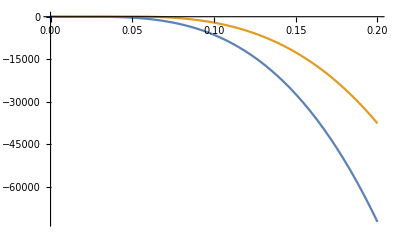

```mathematica
sol=First@NDSolve[{node1,node2,node3,node4,node5,ics}//.params,{v1,v2,v3,v4,v5},{t,0,0.02},Method->{"EquationSimplification"->"Residual"},MaxSteps->100000];
Plot[Evaluate[{v3[t],v4[t]}/. sol],{t,0,0.2},PlotRange->All]
```

```mathematica
Fin=klA (pCO2/H-CO2[t]);
r1=k1 FLB[t]^2 CO2[t]^(1/2);
r2=k2 FLBT[t] ZHU[t];
r3=(k2/KK) FLB[t] ZLA[t];
r4=k3 FLB[t] ZHU[t]^2 CO2[t];
r5=k4 FLB[t] ZHU[t];
params={k1->18.7,k2->0.58,k3->0.09,k4->0.42,KK->34.4,klA->3.3,Ks->115.83,pCO2->0.9,H->737};
```

```mathematica
eqns={FLB'[t]==-2 r1+r2-r3-r4,CO2'[t]==-0.5 r1-r4-0.5 r5+Fin,FLBT'[t]==r1-r2+r3,ZHU'[t]==-r2+r3-2 r4,ZLA'[t]==r2-r3+r5};
eqEqn=Ks FLB[t] ZHU[t]==FLBZHU[t];
ic={FLB[0]==0.444,CO2[0]==0.00123,FLBT[0]==0,ZHU[0]==0.007,ZLA[0]==0};
```

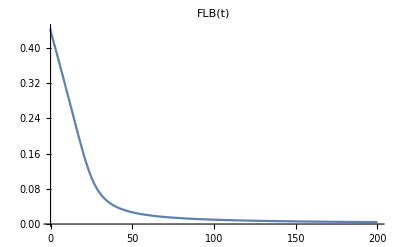
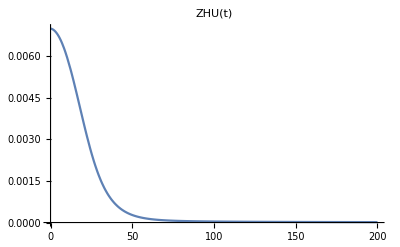
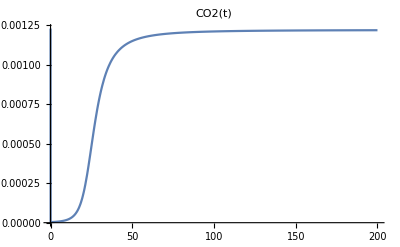
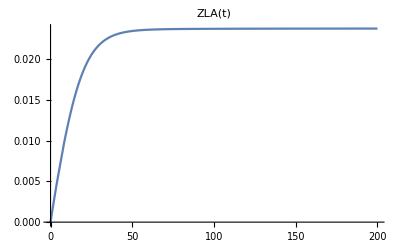

```mathematica
sol=NDSolve[{eqns,eqEqn,ic}/. params,{FLB,ZHU, ,CO2,ZLA},{t,0,200}];
Plot[Evaluate[#[t]/. sol],{t,0,200},PlotRange->All,PlotLabel->#[t]]&/@{FLB,ZHU,CO2,ZLA}
```

```mathematica
NDSolve[{eqns,eqEqn,ic}/. params,{FLB,ZHU, ,CO2,ZLA},{t,0,200},Method->"IndexReduction"->None]
```

{{FLB→InterpolatingFunction[…],ZHU→InterpolatingFunction[…],Null→Null,CO2→InterpolatingFunction[…],ZLA→InterpolatingFunction[…]}}

```mathematica
Clear[u,v,nx,eqn1,eqn2,ic1,ic2,vars,eqn1,eqn2,ic1,ic2,vars,sol,PDEsol,order,p,npts];
npts=100;order=12;p=10;
nx=Range[0,1,1/(npts-1)];
{ddx,d2dx2}=Map[NDSolve`FiniteDifferenceDerivative[Derivative[#],nx,"DifferenceOrder"->order]["DifferentiationMatrix"]&,{1,2}];
u=Array[u$[#][t]&,npts];v=Array[v$[#][t]&,npts];
eqn1=Thread[D[u,t]-D[v,t]==d2dx2.u+u (ddx.v)-v (ddx.u)+(2 π t)^2 v];
eqn2=Thread[d2dx2.v+(2 π t)^2 u==0];
```

```mathematica
eqn1[[{1,-1}]]=Thread[u[[{1,-1}]]==v[[{1,-1}]]];
eqn2[[1]]=v[[1]]==0;
eqn2[[-1]]=ddx[[-1]].v==2 π t Cos[2 π t];
```

```mathematica
ic1=Thread[u==0]/. t->0;
ic2=Thread[v==0]/. t->0;
```

```mathematica
vars=Flatten[{u,v}]/. x__[t]:>x;
PDEsol=First[NDSolve[{eqn1,eqn2,ic1,ic2},vars,{t,0,3},Method->"IndexReduction"->None]];
```

```mathematica
time=Flatten@First[vars[[1]]/. PDEsol];
{usol,vsol}=Flatten[Table[Transpose[{nx,ConstantArray[ti,npts],#/. PDEsol}]/. t->ti,{ti,time[[1]],time[[2]],0.1}],1]&/@{u,v};
GraphicsRow[ListPlot3D[#,PlotRange->All]&/@{usol,vsol},ImageSize->500]
```

-Graphics-

```mathematica
Clear[p,α,β,a,bv,di,bi,ri,nx,grid,nL,order,x,y,dfdx,dfdy,d2fdx2,d2fdy2,Lapf,species,R,eqns,ics,vars,speciesSol,c];
p=1;α=50;β=1000;
bv=Table[If[i<=p,1,-1],{i,2 p}];
di=Table[If[i<=p,1,0.5],{i,2 p}];
a=SparseArray[{{i_,i_}->-1,{i_,j_}/;(i<=p&&j>p)->-0.5 10^-6,{i_,j_}/;(i>p&&j<=p)->10^4},{2 p,2 p}];
bi[x_,y_]:=(1+α x y+β Sin[4 Pi x] Sin[4 Pi y])*bv;
ri[{x_,y_},c_List]:=c*(bi[x,y]+a.c);
nx=N@Range[0,1,1/19];
grid=Flatten[Outer[List,nx,nx],1];
nL=Length[grid];
order=2;
{left,right,bot,top}=Flatten[Position[grid,#]]&/@{{0.,y_},{1.,y_},{x_,0.},{x_,1.}};
```

```mathematica
{dfdx,dfdy,d2fdx2,d2fdy2}=Map[NDSolve`FiniteDifferenceDerivative[#,{nx,nx},"DifferenceOrder"->order]["DifferentiationMatrix"]&,{{1,0},{0,1},{2,0},{0,2}}];
Lapf=d2fdx2+d2fdy2;
```

```mathematica
species=Transpose[Table[Array[c[i][#][t]&,nL],{i,2 p}]];
```

```mathematica
R=Apply[ri,MapThread[List,{grid,species}],1];
eqns=Table[Thread[If[i<=p,1,0]*D[species[[All,i]],t]==R[[All,i]]+di[[i]]*Lapf.species[[All,i]]],{i,2 p}];
Do[eqns[[i]][[left]]=Thread[dfdx[[left]].species[[All,i]]==0];
eqns[[i]][[right]]=Thread[dfdx[[right]].species[[All,i]]==0];
eqns[[i]][[bot]]=Thread[dfdy[[bot]].species[[All,i]]==0];
eqns[[i]][[top]]=Thread[dfdy[[top]].species[[All,i]]==0];,{i,2 p}];
```

```mathematica
ics=Flatten[Table[Thread[(species[[All,i]]/. t->0)==If[i<=p,10+i*(grid/. {x_,y_}:>(16 x (1-x) y (1-y))^2),10^5]],{i,2 p}]];
```

```mathematica
vars=Flatten[species]/. x___[t]:>x;
speciesSol=First[NDSolve[{eqns,ics},vars,{t,0,1},Method->"IndexReduction"->None]];
```

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

```mathematica
csol=(species/. t->0)/. speciesSol;
Row[ListPlot3D[Join[grid,csol[[All,{#}]],2],ImageSize->200]&/@Range[2 p]]
```

-Graphics3D--Graphics3D-

```mathematica
Clear[ve,params,vb,r0,r1,r2,r3,r4,r5,α,β,c1,c2,c3,v23,node1,node2,node3,node4,node5,ics,sol,v1,v2,v3,v4,v5];
ve[t_]:=(4/10) Sin[200 Pi t];
params={vb->6,r0->1000,r1->9000,r2->9000,r3->9000,r4->9000,r5->9000,α->99/100,β->10^-6,c1->10^-6,c2->2 10^-6,c3->3 10^-6};
v23[t_]=β (Exp[(v2[t]-v3[t])/.026]-1);
node1=c1 (v2'[t]-v1'[t])==v1[t]/r0-ve[t]/r0;
node2=c1 (v1'[t]-v2'[t])==(1-α) v23[t]+v2[t]/r1+v2[t]/r2-vb/r2;
node3=c2 v3'[t]==v23[t]-v3[t]/r3;
node4=c3 (v4'[t]-v5'[t])==vb/r4-v4[t]/r4-α v23[t];
node5=c3 (v4'[t]-v5'[t])==v5[t]/r5;
ics={v1[0]==0,v2[0]==vb/2,v3[0]==vb/2,v4[0]==vb,v5[0]==0};
```

```mathematica
sol=First@NDSolve[{node1,node2,node3,node4,node5,ics}//.params,{v1,v2,v3,v4,v5},{t,0,0.02},Method->{"EquationSimplification"->"Residual"},MaxSteps->100000,WorkingPrecision->MachinePrecision];
Plot[Evaluate[{v3[t],v4[t]}/. sol],{t,0,0.2},PlotRange->All]
```

-Graphics-